## Axion off-diagonal couplings to quarks at large σ_0

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]~StringJoin~".."]
```

H:\2_Projects\physics\5d_flavourful_axion

```mathematica
<<"WarpFlavourAxion`"
```

```mathematica
<<"MaTeX`"
```

```mathematica
<<"CustomTicks`"
```

#### Import data

```mathematica
leptonDataAll = <<"output/yukawa_lepton.m";
leptonData =leptonDataAll[[All,1;;2]];
Print["Number of Yn Ye 3x3 matrix pairs (normal hierarchy)"]
Dimensions[leptonData]
```

Number of Yn Ye 3x3 matrix pairs (normal hierarchy)

{1030,2,3,3}

```mathematica
{cMArray,cuData,cdData,ceData}=<<"output/cLcR04.m";
Dimensions/@{cuData,cdData,ceData}
```

{{1321,26,3,2},{1321,26,3,2},{1030,26,3,2}}

```mathematica
leptonAData  =<< "output/A_lepton.m";
Dimensions[leptonAData]
```

{1030,2,3,3}

Check: 
	Lepton data for Y, c and A have the same length

#### Plotting

Plotting parameters

```mathematica
colors=ColorData[97,"ColorList"];
```

Note Xu = - 2 cos^2 β, Xd = - 2 sin^2 β where tan β = 3

```mathematica
tanbeta = 3.; 
Xu = 2. 1^2 / (  1^2 + tanbeta^2 ); 
Xd = 2. tanbeta^2 / (  1^2 + tanbeta^2 );
```

#### Charged Lepton

Second index of AData 1, 2 store AeL, AeR

```mathematica
data=ceData; Dimensions[data]
AData = leptonAData[[All,1;;2]]; Dimensions[AData]
```

{1030,26,3,2}

{1030,2,3,3}

Main data

```mathematica
n = 100;
```

```mathematica
(With[
{kMax = n, cmTotal =Dimensions[data][[2]],
Mpl = 1.22 10^19,zIR=1. 10^10,σ0=3.,X=Xd,Δ=9,
α=0.5},
output=Table[
Mpl /(X ( α AData[[k,2]].
DiagonalMatrix[ Table[ FermionAxionOverlap2[ data[[k, cmpt, whichQuark, 2]] ,Δ,σ0, zIR],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,2]] ] - (* - for F_V, + for F_A *)
(1-α) AData[[k,1]].
DiagonalMatrix[ Table[ FermionAxionOverlap2[ data[[k, cmpt, whichQuark, 1]] ,Δ,σ0, zIR],{whichQuark,3}] ].
ConjugateTranspose[ AData[[k,1]] ] ) ),
{k,kMax},{cmpt,cmTotal}]
]//AbsoluteTiming)[[1]]
```

31.7401

```mathematica
y12= Table[Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,2]] ]]],{cmpt,Dimensions[data][[2]]}];
y13= Table[Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,1,3]] ]]],{cmpt,Dimensions[data][[2]]}];
y23= Table[Through[{Mean,StandardDeviation}[ Log10/@Abs[output[[All,cmpt,2,3]] ]]],{cmpt,Dimensions[data][[2]]}];
```

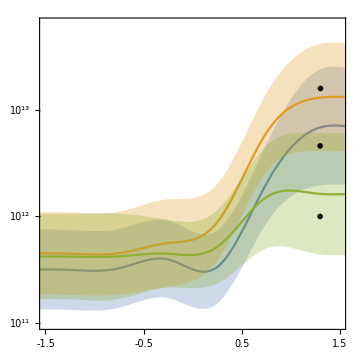

```mathematica
SetOptions[ListPlot, Joined->True,Frame->True,InterpolationOrder->3,AspectRatio->1,ImageSize->Medium];
fig = With[{cmmin=-1.5,cmmax=1.5,fvmin=11,fvmax=13.8},
Show[
ListPlot[
(* Also plot 1σ range *)
{{cMArray,#[[All, 1]]}//Transpose, {cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose, {cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
(* Setup options *)
PlotRange->{{cmmin,cmmax},{fvmin,fvmax}},
FrameTicks->{{LogTicks,StripTickLabels[LogTicks]},{LinTicks,StripTickLabels[LinTicks]}},
FrameLabel->{MaTeX["c_M"],MaTeX["F_V"]}, (* Replace for F_V *)
PlotStyle->{colors[[1]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.3],colors[[1]]]
]& @ y12,

ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
PlotStyle->{colors[[2]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.3],colors[[2]]]
]& @ y13,

ListPlot[{{cMArray,#[[All, 1]]}//Transpose,{cMArray,#[[All, 1]]-#[[All, 2]]}//Transpose,{cMArray,#[[All, 1]]+#[[All, 2]]}//Transpose},
PlotStyle->{colors[[3]],Opacity[0],Opacity[0]},
Filling->{2->{3}},FillingStyle->Directive[Opacity[0.3],colors[[3]]]
]& @ y23,

(* Labels for curve *)
Epilog->MapThread[Inset[#1,{#2,#3}]&,
{{MaTeX["F_{e \mu}"],MaTeX["F_{e t}"],MaTeX["F_{\mu t}"]
},
{1.3,1.3,1.3
},
{12.66,13.2,12.00
}}
]
]
]
```